```mathematica
EdgesInColor[edges_,color_]:=Map[#->Directive[color,Thick]&,edges]
```

```mathematica
EdgesInColor2[assoc_,edges_,color_]:=Block[{result=assoc},
Table[
If[KeyExistsQ[result,e],
result[e]=Join[result[e],color]
,
result[e]=color
]
,{e,edges}
];
result
]
```

```mathematica
BlurAssoc[assoc_]:=Block[{result=assoc},
Table[
result[k]=If[Length[result[k]]>2,{Brown},If[Length[result[k]]>1,{Purple},result[k]]]
,{k,Keys[result]}
];
result]
```

```mathematica
AssocToRule[assoc_]:=Table[
k->assoc[k]
,{k,Keys[assoc]}
]
```

```mathematica
QuadrilateralsWithPattern[7,5]//Length
```

16

v16ax247bx359x8c

v16ax247bx359x8c

v16ax247bx359x8c

«1 more identical outputs»

v147bx26ax359x8c

v147bx26ax359x8c

v16ax247bx359x8c

v16ax247bx359x8c

v16ax247bx359x8c

«3 more identical outputs»

v147bx26ax359x8c

v147bx26ax359x8c

v16ax247bx359x8c

v147bx26ax359x8c

v146ax27bx359x8c

v17bx246ax359x8c

v146ax27bx359x8c

v146ax27bx359x8c

v17bx246ax359x8c

v17bx246ax359x8c

v17bx246ax359x8c

«3 more identical outputs»

v146ax27bx359x8c

v146ax27bx359x8c

v17bx246ax359x8c

v17bx246ax359x8c

v17bx246ax359x8c

«1 more identical outputs»

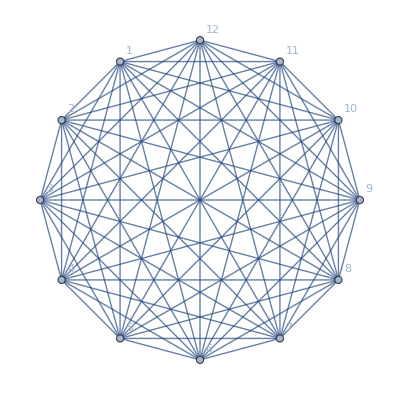
{-Graphics-139♁26a♁47b♁58c
16a♁249♁37b♁58c
16a♁27b♁359♁48c
149♁26a♁37b♁58c
16a♁259♁37b♁48c
8
{16a♁27b♁359♁48c,16a♁259♁37b♁48c,16a♁247b♁39♁58c,16a♁249♁37b♁58c,16a♁247b♁359♁8c,149♁26a♁37b♁58c,139♁26a♁47b♁58c,139♁247b♁58c♁6a},-Graphics-139♁26a♁47b♁58c
16a♁249♁37b♁58c
16a♁27b♁359♁48c
149♁26a♁37b♁58c
17b♁259♁36a♁48c
29
{19♁247b♁36a♁58c,17b♁26a♁359♁48c,17b♁259♁36a♁48c,17b♁249♁36a♁58c,16a♁27b♁359♁48c,16a♁259♁37b♁48c,16a♁247b♁39♁58c,16a♁249♁37b♁58c,16a♁247b♁359♁8c,147b♁29♁36a♁58c,149♁27b♁36a♁58c,147b♁26a♁39♁58c,149♁26a♁37b♁58c,147b♁26a♁359♁8c,147b♁259♁36a♁8c,136a♁29♁47b♁58c,136a♁27b♁49♁58c,136a♁27b♁48c♁59,137b♁26a♁49♁58c,137b♁26a♁48c♁59,139♁26a♁47b♁58c,137b♁259♁48c♁6a,136a♁259♁48c♁7b,136a♁259♁47b♁8c,136a♁247b♁59♁8c,136a♁247b♁58c,137b♁249♁58c♁6a,136a♁249♁58c♁7b,139♁247b♁58c♁6a},-Graphics-139♁26a♁47b♁58c
16a♁249♁37b♁58c
16a♁27b♁359♁48c
149♁27b♁36a♁58c
16a♁259♁37b♁48c
18
{19♁247b♁36a♁58c,16a♁27b♁359♁48c,16a♁259♁37b♁48c,16a♁247b♁39♁58c,16a♁249♁37b♁58c,16a♁247b♁359♁8c,149♁27b♁36a♁58c,149♁26a♁37b♁58c,136a♁29♁47b♁58c,136a♁27b♁49♁58c,136a♁27b♁48c♁59,139♁26a♁47b♁58c,136a♁259♁48c♁7b,136a♁259♁47b♁8c,136a♁247b♁59♁8c,136a♁247b♁58c,136a♁249♁58c♁7b,139♁247b♁58c♁6a},-Graphics-139♁26a♁47b♁58c
16a♁249♁37b♁58c
16a♁27b♁359♁48c
149♁27b♁36a♁58c
17b♁259♁36a♁48c
29
{19♁247b♁36a♁58c,17b♁26a♁359♁48c,17b♁259♁36a♁48c,17b♁249♁36a♁58c,16a♁27b♁359♁48c,16a♁259♁37b♁48c,16a♁247b♁39♁58c,16a♁249♁37b♁58c,16a♁247b♁359♁8c,147b♁29♁36a♁58c,149♁27b♁36a♁58c,147b♁26a♁39♁58c,149♁26a♁37b♁58c,147b♁26a♁359♁8c,147b♁259♁36a♁8c,136a♁29♁47b♁58c,136a♁27b♁49♁58c,136a♁27b♁48c♁59,137b♁26a♁49♁58c,137b♁26a♁48c♁59,139♁26a♁47b♁58c,137b♁259♁48c♁6a,136a♁259♁48c♁7b,136a♁259♁47b♁8c,136a♁247b♁59♁8c,136a♁247b♁58c,137b♁249♁58c♁6a,136a♁249♁58c♁7b,139♁247b♁58c♁6a},-Graphics-139♁26a♁47b♁58c
16a♁249♁37b♁58c
17b♁26a♁359♁48c
149♁26a♁37b♁58c
16a♁259♁37b♁48c
11
{17b♁26a♁359♁48c,16a♁259♁37b♁48c,16a♁249♁37b♁58c,147b♁26a♁39♁58c,149♁26a♁37b♁58c,147b♁26a♁359♁8c,137b♁26a♁49♁58c,137b♁26a♁48c♁59,139♁26a♁47b♁58c,137b♁259♁48c♁6a,137b♁249♁58c♁6a},-Graphics-139♁26a♁47b♁58c
16a♁249♁37b♁58c
17b♁26a♁359♁48c
149♁26a♁37b♁58c
17b♁259♁36a♁48c
19
{17b♁26a♁359♁48c,17b♁259♁36a♁48c,17b♁249♁36a♁58c,16a♁259♁37b♁48c,16a♁249♁37b♁58c,147b♁29♁36a♁58c,147b♁26a♁39♁58c,149♁26a♁37b♁58c,147b♁26a♁359♁8c,147b♁259♁36a♁8c,136a♁29♁47b♁58c,137b♁26a♁49♁58c,137b♁26a♁48c♁59,139♁26a♁47b♁58c,137b♁259♁48c♁6a,136a♁259♁48c♁7b,136a♁259♁47b♁8c,137b♁249♁58c♁6a,136a♁249♁58c♁7b},-Graphics-139♁26a♁47b♁58c
16a♁249♁37b♁58c
17b♁26a♁359♁48c
149♁27b♁36a♁58c
16a♁259♁37b♁48c
29
{19♁247b♁36a♁58c,17b♁26a♁359♁48c,17b♁259♁36a♁48c,17b♁249♁36a♁58c,16a♁27b♁359♁48c,16a♁259♁37b♁48c,16a♁247b♁39♁58c,16a♁249♁37b♁58c,16a♁247b♁359♁8c,147b♁29♁36a♁58c,149♁27b♁36a♁58c,147b♁26a♁39♁58c,149♁26a♁37b♁58c,147b♁26a♁359♁8c,147b♁259♁36a♁8c,136a♁29♁47b♁58c,136a♁27b♁49♁58c,136a♁27b♁48c♁59,137b♁26a♁49♁58c,137b♁26a♁48c♁59,139♁26a♁47b♁58c,137b♁259♁48c♁6a,136a♁259♁48c♁7b,136a♁259♁47b♁8c,136a♁247b♁59♁8c,136a♁247b♁58c,137b♁249♁58c♁6a,136a♁249♁58c♁7b,139♁247b♁58c♁6a},-Graphics-139♁26a♁47b♁58c
16a♁249♁37b♁58c
17b♁26a♁359♁48c
149♁27b♁36a♁58c
17b♁259♁36a♁48c
29
{19♁247b♁36a♁58c,17b♁26a♁359♁48c,17b♁259♁36a♁48c,17b♁249♁36a♁58c,16a♁27b♁359♁48c,16a♁259♁37b♁48c,16a♁247b♁39♁58c,16a♁249♁37b♁58c,16a♁247b♁359♁8c,147b♁29♁36a♁58c,149♁27b♁36a♁58c,147b♁26a♁39♁58c,149♁26a♁37b♁58c,147b♁26a♁359♁8c,147b♁259♁36a♁8c,136a♁29♁47b♁58c,136a♁27b♁49♁58c,136a♁27b♁48c♁59,137b♁26a♁49♁58c,137b♁26a♁48c♁59,139♁26a♁47b♁58c,137b♁259♁48c♁6a,136a♁259♁48c♁7b,136a♁259♁47b♁8c,136a♁247b♁59♁8c,136a♁247b♁58c,137b♁249♁58c♁6a,136a♁249♁58c♁7b,139♁247b♁58c♁6a},-Graphics-139♁26a♁47b♁58c
17b♁249♁36a♁58c
16a♁27b♁359♁48c
149♁26a♁37b♁58c
16a♁259♁37b♁48c
29
{19♁247b♁36a♁58c,17b♁26a♁359♁48c,17b♁259♁36a♁48c,17b♁249♁36a♁58c,16a♁27b♁359♁48c,16a♁259♁37b♁48c,16a♁247b♁39♁58c,16a♁249♁37b♁58c,16a♁247b♁359♁8c,147b♁29♁36a♁58c,149♁27b♁36a♁58c,147b♁26a♁39♁58c,149♁26a♁37b♁58c,147b♁26a♁359♁8c,147b♁259♁36a♁8c,136a♁29♁47b♁58c,136a♁27b♁49♁58c,136a♁27b♁48c♁59,137b♁26a♁49♁58c,137b♁26a♁48c♁59,139♁26a♁47b♁58c,137b♁259♁48c♁6a,136a♁259♁48c♁7b,136a♁259♁47b♁8c,136a♁247b♁59♁8c,136a♁247b♁58c,137b♁249♁58c♁6a,136a♁249♁58c♁7b,139♁247b♁58c♁6a},-Graphics-139♁26a♁47b♁58c
17b♁249♁36a♁58c
16a♁27b♁359♁48c
149♁26a♁37b♁58c
17b♁259♁36a♁48c
29
{19♁247b♁36a♁58c,17b♁26a♁359♁48c,17b♁259♁36a♁48c,17b♁249♁36a♁58c,16a♁27b♁359♁48c,16a♁259♁37b♁48c,16a♁247b♁39♁58c,16a♁249♁37b♁58c,16a♁247b♁359♁8c,147b♁29♁36a♁58c,149♁27b♁36a♁58c,147b♁26a♁39♁58c,149♁26a♁37b♁58c,147b♁26a♁359♁8c,147b♁259♁36a♁8c,136a♁29♁47b♁58c,136a♁27b♁49♁58c,136a♁27b♁48c♁59,137b♁26a♁49♁58c,137b♁26a♁48c♁59,139♁26a♁47b♁58c,137b♁259♁48c♁6a,136a♁259♁48c♁7b,136a♁259♁47b♁8c,136a♁247b♁59♁8c,136a♁247b♁58c,137b♁249♁58c♁6a,136a♁249♁58c♁7b,139♁247b♁58c♁6a},-Graphics-139♁26a♁47b♁58c
17b♁249♁36a♁58c
16a♁27b♁359♁48c
149♁27b♁36a♁58c
16a♁259♁37b♁48c
29
{19♁247b♁36a♁58c,17b♁26a♁359♁48c,17b♁259♁36a♁48c,17b♁249♁36a♁58c,16a♁27b♁359♁48c,16a♁259♁37b♁48c,16a♁247b♁39♁58c,16a♁249♁37b♁58c,16a♁247b♁359♁8c,147b♁29♁36a♁58c,149♁27b♁36a♁58c,147b♁26a♁39♁58c,149♁26a♁37b♁58c,147b♁26a♁359♁8c,147b♁259♁36a♁8c,136a♁29♁47b♁58c,136a♁27b♁49♁58c,136a♁27b♁48c♁59,137b♁26a♁49♁58c,137b♁26a♁48c♁59,139♁26a♁47b♁58c,137b♁259♁48c♁6a,136a♁259♁48c♁7b,136a♁259♁47b♁8c,136a♁247b♁59♁8c,136a♁247b♁58c,137b♁249♁58c♁6a,136a♁249♁58c♁7b,139♁247b♁58c♁6a},-Graphics-139♁26a♁47b♁58c
17b♁249♁36a♁58c
16a♁27b♁359♁48c
149♁27b♁36a♁58c
17b♁259♁36a♁48c
22
{19♁247b♁36a♁58c,17b♁26a♁359♁48c,17b♁259♁36a♁48c,17b♁249♁36a♁58c,16a♁27b♁359♁48c,16a♁247b♁39♁58c,16a♁247b♁359♁8c,147b♁29♁36a♁58c,149♁27b♁36a♁58c,147b♁26a♁39♁58c,147b♁26a♁359♁8c,147b♁259♁36a♁8c,136a♁29♁47b♁58c,136a♁27b♁49♁58c,136a♁27b♁48c♁59,139♁26a♁47b♁58c,136a♁259♁48c♁7b,136a♁259♁47b♁8c,136a♁247b♁59♁8c,136a♁247b♁58c,136a♁249♁58c♁7b,139♁247b♁58c♁6a},-Graphics-139♁26a♁47b♁58c
17b♁249♁36a♁58c
17b♁26a♁359♁48c
149♁26a♁37b♁58c
16a♁259♁37b♁48c
19
{17b♁26a♁359♁48c,17b♁259♁36a♁48c,17b♁249♁36a♁58c,16a♁259♁37b♁48c,16a♁249♁37b♁58c,147b♁29♁36a♁58c,147b♁26a♁39♁58c,149♁26a♁37b♁58c,147b♁26a♁359♁8c,147b♁259♁36a♁8c,136a♁29♁47b♁58c,137b♁26a♁49♁58c,137b♁26a♁48c♁59,139♁26a♁47b♁58c,137b♁259♁48c♁6a,136a♁259♁48c♁7b,136a♁259♁47b♁8c,137b♁249♁58c♁6a,136a♁249♁58c♁7b},-Graphics-139♁26a♁47b♁58c
17b♁249♁36a♁58c
17b♁26a♁359♁48c
149♁26a♁37b♁58c
17b♁259♁36a♁48c
13
{17b♁26a♁359♁48c,17b♁259♁36a♁48c,17b♁249♁36a♁58c,147b♁29♁36a♁58c,147b♁26a♁39♁58c,149♁26a♁37b♁58c,147b♁26a♁359♁8c,147b♁259♁36a♁8c,137b♁26a♁49♁58c,137b♁26a♁48c♁59,139♁26a♁47b♁58c,137b♁259♁48c♁6a,137b♁249♁58c♁6a},-Graphics-139♁26a♁47b♁58c
17b♁249♁36a♁58c
17b♁26a♁359♁48c
149♁27b♁36a♁58c
16a♁259♁37b♁48c
29
{19♁247b♁36a♁58c,17b♁26a♁359♁48c,17b♁259♁36a♁48c,17b♁249♁36a♁58c,16a♁27b♁359♁48c,16a♁259♁37b♁48c,16a♁247b♁39♁58c,16a♁249♁37b♁58c,16a♁247b♁359♁8c,147b♁29♁36a♁58c,149♁27b♁36a♁58c,147b♁26a♁39♁58c,149♁26a♁37b♁58c,147b♁26a♁359♁8c,147b♁259♁36a♁8c,136a♁29♁47b♁58c,136a♁27b♁49♁58c,136a♁27b♁48c♁59,137b♁26a♁49♁58c,137b♁26a♁48c♁59,139♁26a♁47b♁58c,137b♁259♁48c♁6a,136a♁259♁48c♁7b,136a♁259♁47b♁8c,136a♁247b♁59♁8c,136a♁247b♁58c,137b♁249♁58c♁6a,136a♁249♁58c♁7b,139♁247b♁58c♁6a},-Graphics-139♁26a♁47b♁58c
17b♁249♁36a♁58c
17b♁26a♁359♁48c
149♁27b♁36a♁58c
17b♁259♁36a♁48c
11
{19♁247b♁36a♁58c,17b♁26a♁359♁48c,17b♁259♁36a♁48c,17b♁249♁36a♁58c,147b♁29♁36a♁58c,149♁27b♁36a♁58c,147b♁26a♁39♁58c,147b♁26a♁359♁8c,147b♁259♁36a♁8c,139♁26a♁47b♁58c,139♁247b♁58c♁6a},-Graphics-139♁27b♁46a♁58c
16a♁249♁37b♁58c
16a♁27b♁359♁48c
149♁26a♁37b♁58c
16a♁259♁37b♁48c
11
{19♁246a♁37b♁58c,16a♁27b♁359♁48c,16a♁259♁37b♁48c,16a♁249♁37b♁58c,146a♁29♁37b♁58c,146a♁27b♁39♁58c,146a♁27b♁359♁8c,149♁26a♁37b♁58c,146a♁259♁37b♁8c,139♁27b♁46a♁58c,139♁246a♁58c♁7b},-Graphics-139♁27b♁46a♁58c
16a♁249♁37b♁58c
16a♁27b♁359♁48c
149♁26a♁37b♁58c
17b♁259♁36a♁48c
29
{19♁246a♁37b♁58c,17b♁26a♁359♁48c,17b♁259♁36a♁48c,17b♁246a♁39♁58c,17b♁249♁36a♁58c,17b♁246a♁359♁8c,16a♁27b♁359♁48c,16a♁259♁37b♁48c,16a♁249♁37b♁58c,146a♁29♁37b♁58c,146a♁27b♁39♁58c,149♁27b♁36a♁58c,146a♁27b♁359♁8c,149♁26a♁37b♁58c,146a♁259♁37b♁8c,137b♁29♁46a♁58c,136a♁27b♁49♁58c,136a♁27b♁48c♁59,139♁27b♁46a♁58c,137b♁26a♁49♁58c,137b♁26a♁48c♁59,137b♁259♁48c♁6a,136a♁259♁48c♁7b,137b♁259♁46a♁8c,137b♁246a♁59♁8c,137b♁246a♁58c,137b♁249♁58c♁6a,136a♁249♁58c♁7b,139♁246a♁58c♁7b},-Graphics-139♁27b♁46a♁58c
16a♁249♁37b♁58c
16a♁27b♁359♁48c
149♁27b♁36a♁58c
16a♁259♁37b♁48c
13
{16a♁27b♁359♁48c,16a♁259♁37b♁48c,16a♁249♁37b♁58c,146a♁29♁37b♁58c,146a♁27b♁39♁58c,149♁27b♁36a♁58c,146a♁27b♁359♁8c,146a♁259♁37b♁8c,136a♁27b♁49♁58c,136a♁27b♁48c♁59,139♁27b♁46a♁58c,136a♁259♁48c♁7b,136a♁249♁58c♁7b},-Graphics-139♁27b♁46a♁58c
16a♁249♁37b♁58c
16a♁27b♁359♁48c
149♁27b♁36a♁58c
17b♁259♁36a♁48c
19
{17b♁259♁36a♁48c,17b♁249♁36a♁58c,16a♁27b♁359♁48c,16a♁259♁37b♁48c,16a♁249♁37b♁58c,146a♁29♁37b♁58c,146a♁27b♁39♁58c,149♁27b♁36a♁58c,146a♁27b♁359♁8c,146a♁259♁37b♁8c,137b♁29♁46a♁58c,136a♁27b♁49♁58c,136a♁27b♁48c♁59,139♁27b♁46a♁58c,137b♁259♁48c♁6a,136a♁259♁48c♁7b,137b♁259♁46a♁8c,137b♁249♁58c♁6a,136a♁249♁58c♁7b},-Graphics-139♁27b♁46a♁58c
16a♁249♁37b♁58c
17b♁26a♁359♁48c
149♁26a♁37b♁58c
16a♁259♁37b♁48c
22
{19♁246a♁37b♁58c,17b♁26a♁359♁48c,17b♁246a♁39♁58c,17b♁246a♁359♁8c,16a♁27b♁359♁48c,16a♁259♁37b♁48c,16a♁249♁37b♁58c,146a♁29♁37b♁58c,146a♁27b♁39♁58c,146a♁27b♁359♁8c,149♁26a♁37b♁58c,146a♁259♁37b♁8c,137b♁29♁46a♁58c,139♁27b♁46a♁58c,137b♁26a♁49♁58c,137b♁26a♁48c♁59,137b♁259♁48c♁6a,137b♁259♁46a♁8c,137b♁246a♁59♁8c,137b♁246a♁58c,137b♁249♁58c♁6a,139♁246a♁58c♁7b},-Graphics-139♁27b♁46a♁58c
16a♁249♁37b♁58c
17b♁26a♁359♁48c
149♁26a♁37b♁58c
17b♁259♁36a♁48c
29
{19♁246a♁37b♁58c,17b♁26a♁359♁48c,17b♁259♁36a♁48c,17b♁246a♁39♁58c,17b♁249♁36a♁58c,17b♁246a♁359♁8c,16a♁27b♁359♁48c,16a♁259♁37b♁48c,16a♁249♁37b♁58c,146a♁29♁37b♁58c,146a♁27b♁39♁58c,149♁27b♁36a♁58c,146a♁27b♁359♁8c,149♁26a♁37b♁58c,146a♁259♁37b♁8c,137b♁29♁46a♁58c,136a♁27b♁49♁58c,136a♁27b♁48c♁59,139♁27b♁46a♁58c,137b♁26a♁49♁58c,137b♁26a♁48c♁59,137b♁259♁48c♁6a,136a♁259♁48c♁7b,137b♁259♁46a♁8c,137b♁246a♁59♁8c,137b♁246a♁58c,137b♁249♁58c♁6a,136a♁249♁58c♁7b,139♁246a♁58c♁7b},-Graphics-139♁27b♁46a♁58c
16a♁249♁37b♁58c
17b♁26a♁359♁48c
149♁27b♁36a♁58c
16a♁259♁37b♁48c
29
{19♁246a♁37b♁58c,17b♁26a♁359♁48c,17b♁259♁36a♁48c,17b♁246a♁39♁58c,17b♁249♁36a♁58c,17b♁246a♁359♁8c,16a♁27b♁359♁48c,16a♁259♁37b♁48c,16a♁249♁37b♁58c,146a♁29♁37b♁58c,146a♁27b♁39♁58c,149♁27b♁36a♁58c,146a♁27b♁359♁8c,149♁26a♁37b♁58c,146a♁259♁37b♁8c,137b♁29♁46a♁58c,136a♁27b♁49♁58c,136a♁27b♁48c♁59,139♁27b♁46a♁58c,137b♁26a♁49♁58c,137b♁26a♁48c♁59,137b♁259♁48c♁6a,136a♁259♁48c♁7b,137b♁259♁46a♁8c,137b♁246a♁59♁8c,137b♁246a♁58c,137b♁249♁58c♁6a,136a♁249♁58c♁7b,139♁246a♁58c♁7b},-Graphics-139♁27b♁46a♁58c
16a♁249♁37b♁58c
17b♁26a♁359♁48c
149♁27b♁36a♁58c
17b♁259♁36a♁48c
29
{19♁246a♁37b♁58c,17b♁26a♁359♁48c,17b♁259♁36a♁48c,17b♁246a♁39♁58c,17b♁249♁36a♁58c,17b♁246a♁359♁8c,16a♁27b♁359♁48c,16a♁259♁37b♁48c,16a♁249♁37b♁58c,146a♁29♁37b♁58c,146a♁27b♁39♁58c,149♁27b♁36a♁58c,146a♁27b♁359♁8c,149♁26a♁37b♁58c,146a♁259♁37b♁8c,137b♁29♁46a♁58c,136a♁27b♁49♁58c,136a♁27b♁48c♁59,139♁27b♁46a♁58c,137b♁26a♁49♁58c,137b♁26a♁48c♁59,137b♁259♁48c♁6a,136a♁259♁48c♁7b,137b♁259♁46a♁8c,137b♁246a♁59♁8c,137b♁246a♁58c,137b♁249♁58c♁6a,136a♁249♁58c♁7b,139♁246a♁58c♁7b},-Graphics-139♁27b♁46a♁58c
17b♁249♁36a♁58c
16a♁27b♁359♁48c
149♁26a♁37b♁58c
16a♁259♁37b♁48c
29
{19♁246a♁37b♁58c,17b♁26a♁359♁48c,17b♁259♁36a♁48c,17b♁246a♁39♁58c,17b♁249♁36a♁58c,17b♁246a♁359♁8c,16a♁27b♁359♁48c,16a♁259♁37b♁48c,16a♁249♁37b♁58c,146a♁29♁37b♁58c,146a♁27b♁39♁58c,149♁27b♁36a♁58c,146a♁27b♁359♁8c,149♁26a♁37b♁58c,146a♁259♁37b♁8c,137b♁29♁46a♁58c,136a♁27b♁49♁58c,136a♁27b♁48c♁59,139♁27b♁46a♁58c,137b♁26a♁49♁58c,137b♁26a♁48c♁59,137b♁259♁48c♁6a,136a♁259♁48c♁7b,137b♁259♁46a♁8c,137b♁246a♁59♁8c,137b♁246a♁58c,137b♁249♁58c♁6a,136a♁249♁58c♁7b,139♁246a♁58c♁7b},-Graphics-139♁27b♁46a♁58c
17b♁249♁36a♁58c
16a♁27b♁359♁48c
149♁26a♁37b♁58c
17b♁259♁36a♁48c
29
{19♁246a♁37b♁58c,17b♁26a♁359♁48c,17b♁259♁36a♁48c,17b♁246a♁39♁58c,17b♁249♁36a♁58c,17b♁246a♁359♁8c,16a♁27b♁359♁48c,16a♁259♁37b♁48c,16a♁249♁37b♁58c,146a♁29♁37b♁58c,146a♁27b♁39♁58c,149♁27b♁36a♁58c,146a♁27b♁359♁8c,149♁26a♁37b♁58c,146a♁259♁37b♁8c,137b♁29♁46a♁58c,136a♁27b♁49♁58c,136a♁27b♁48c♁59,139♁27b♁46a♁58c,137b♁26a♁49♁58c,137b♁26a♁48c♁59,137b♁259♁48c♁6a,136a♁259♁48c♁7b,137b♁259♁46a♁8c,137b♁246a♁59♁8c,137b♁246a♁58c,137b♁249♁58c♁6a,136a♁249♁58c♁7b,139♁246a♁58c♁7b},-Graphics-139♁27b♁46a♁58c
17b♁249♁36a♁58c
16a♁27b♁359♁48c
149♁27b♁36a♁58c
16a♁259♁37b♁48c
19
{17b♁259♁36a♁48c,17b♁249♁36a♁58c,16a♁27b♁359♁48c,16a♁259♁37b♁48c,16a♁249♁37b♁58c,146a♁29♁37b♁58c,146a♁27b♁39♁58c,149♁27b♁36a♁58c,146a♁27b♁359♁8c,146a♁259♁37b♁8c,137b♁29♁46a♁58c,136a♁27b♁49♁58c,136a♁27b♁48c♁59,139♁27b♁46a♁58c,137b♁259♁48c♁6a,136a♁259♁48c♁7b,137b♁259♁46a♁8c,137b♁249♁58c♁6a,136a♁249♁58c♁7b},-Graphics-139♁27b♁46a♁58c
17b♁249♁36a♁58c
16a♁27b♁359♁48c
149♁27b♁36a♁58c
17b♁259♁36a♁48c
11
{17b♁259♁36a♁48c,17b♁249♁36a♁58c,16a♁27b♁359♁48c,146a♁27b♁39♁58c,149♁27b♁36a♁58c,146a♁27b♁359♁8c,136a♁27b♁49♁58c,136a♁27b♁48c♁59,139♁27b♁46a♁58c,136a♁259♁48c♁7b,136a♁249♁58c♁7b},-Graphics-139♁27b♁46a♁58c
17b♁249♁36a♁58c
17b♁26a♁359♁48c
149♁26a♁37b♁58c
16a♁259♁37b♁48c
29
{19♁246a♁37b♁58c,17b♁26a♁359♁48c,17b♁259♁36a♁48c,17b♁246a♁39♁58c,17b♁249♁36a♁58c,17b♁246a♁359♁8c,16a♁27b♁359♁48c,16a♁259♁37b♁48c,16a♁249♁37b♁58c,146a♁29♁37b♁58c,146a♁27b♁39♁58c,149♁27b♁36a♁58c,146a♁27b♁359♁8c,149♁26a♁37b♁58c,146a♁259♁37b♁8c,137b♁29♁46a♁58c,136a♁27b♁49♁58c,136a♁27b♁48c♁59,139♁27b♁46a♁58c,137b♁26a♁49♁58c,137b♁26a♁48c♁59,137b♁259♁48c♁6a,136a♁259♁48c♁7b,137b♁259♁46a♁8c,137b♁246a♁59♁8c,137b♁246a♁58c,137b♁249♁58c♁6a,136a♁249♁58c♁7b,139♁246a♁58c♁7b},-Graphics-139♁27b♁46a♁58c
17b♁249♁36a♁58c
17b♁26a♁359♁48c
149♁26a♁37b♁58c
17b♁259♁36a♁48c
18
{19♁246a♁37b♁58c,17b♁26a♁359♁48c,17b♁259♁36a♁48c,17b♁246a♁39♁58c,17b♁249♁36a♁58c,17b♁246a♁359♁8c,149♁27b♁36a♁58c,149♁26a♁37b♁58c,137b♁29♁46a♁58c,139♁27b♁46a♁58c,137b♁26a♁49♁58c,137b♁26a♁48c♁59,137b♁259♁48c♁6a,137b♁259♁46a♁8c,137b♁246a♁59♁8c,137b♁246a♁58c,137b♁249♁58c♁6a,139♁246a♁58c♁7b},-Graphics-139♁27b♁46a♁58c
17b♁249♁36a♁58c
17b♁26a♁359♁48c
149♁27b♁36a♁58c
16a♁259♁37b♁48c
29
{19♁246a♁37b♁58c,17b♁26a♁359♁48c,17b♁259♁36a♁48c,17b♁246a♁39♁58c,17b♁249♁36a♁58c,17b♁246a♁359♁8c,16a♁27b♁359♁48c,16a♁259♁37b♁48c,16a♁249♁37b♁58c,146a♁29♁37b♁58c,146a♁27b♁39♁58c,149♁27b♁36a♁58c,146a♁27b♁359♁8c,149♁26a♁37b♁58c,146a♁259♁37b♁8c,137b♁29♁46a♁58c,136a♁27b♁49♁58c,136a♁27b♁48c♁59,139♁27b♁46a♁58c,137b♁26a♁49♁58c,137b♁26a♁48c♁59,137b♁259♁48c♁6a,136a♁259♁48c♁7b,137b♁259♁46a♁8c,137b♁246a♁59♁8c,137b♁246a♁58c,137b♁249♁58c♁6a,136a♁249♁58c♁7b,139♁246a♁58c♁7b},-Graphics-139♁27b♁46a♁58c
17b♁249♁36a♁58c
17b♁26a♁359♁48c
149♁27b♁36a♁58c
17b♁259♁36a♁48c
8
{17b♁26a♁359♁48c,17b♁259♁36a♁48c,17b♁246a♁39♁58c,17b♁249♁36a♁58c,17b♁246a♁359♁8c,149♁27b♁36a♁58c,139♁27b♁46a♁58c,139♁246a♁58c♁7b}}

```mathematica
With[
{nodes=12},
Monitor[
Flatten[
Table[
Table[
Table[
Table[
Table[
Block[
{
e1=EdgeList[GraphComplement[GraphFromSets[part1]]],
e2=EdgeList[GraphComplement[GraphFromSets[part2]]],
e3=EdgeList[GraphComplement[GraphFromSets[part3]]],
e4=EdgeList[GraphComplement[GraphFromSets[part4]]],
e5=EdgeList[GraphComplement[GraphFromSets[part5]]],
colors=Association[]
},
colors=EdgesInColor2[colors,e1,{Yellow}];
colors=EdgesInColor2[colors,e2,{Red}];
colors=EdgesInColor2[colors,e3,{Darker[Green]}];
colors=EdgesInColor2[colors,e4,{Blue}];
colors=EdgesInColor2[colors,e5,{Orange}];
colors=BlurAssoc[colors];
Block[
{
gf=Select[FindFullFormula[ EdgeDelete[CompleteGraph[nodes],DeleteDuplicates[Join[e1,e2,e3,e4,e5]]]], SymbolLevel[#]==4&],
first,
efirst
},
first=First[Select[gf,HasTrianglePattern[SymbolToSets[#]]&]];
efirst=EdgeList[GraphComplement[GraphFromSets[SymbolToSets[first]]]];
Print[first];
colors=EdgesInColor2[colors,efirst,{Thickness[0.05]}];
Labeled[
CompleteGraph[nodes,
EdgeStyle->AssocToRule[colors],
VertexLabels->"Name",
ImageSize->400
],
Column[{Style[SetsToLabel[part1],Darker[Yellow]],Style[SetsToLabel[part2],Red],Style[SetsToLabel[part3],Darker[Green]],Style[SetsToLabel[part4],Blue],Style[SetsToLabel[part5],Orange],
Length[gf],
Map[With[{s=SymbolToSets[#]},Style[SetsToLabel2[s],If[HasQuadrilateralPattern[s],Blue,If[HasTrianglePattern[s],Red,Black]]]]&,gf]}]
]
]
],
{part5,Take[QuadrilateralsWithPattern[nodes,5],2]}
],
{part4,Take[QuadrilateralsWithPattern[nodes,4],2]}
],
{part3,Take[QuadrilateralsWithPattern[nodes,3],2]}
],
{part2,Take[QuadrilateralsWithPattern[nodes,2],2]}
],
{part1,Take[QuadrilateralsWithPattern[nodes,1],2]}
],5],
{part1,part2,part3,part4,part5}
]
]
```

```mathematica
{Thick}
```

{Thickness[Large]}